## ElectricalGridSocketImages

```mathematica
CountryData["Hong Kong","ElectricalGridSocketImages"]
```

{-Graphics-,-Graphics-}

```mathematica
CountryData["Australia","ElectricalGridSocketImages"]
```

{-Graphics-}

```mathematica
CountryData["America","ElectricalGridSocketImages"]
```

{-Graphics-}

```mathematica
CountryData["China","ElectricalGridSocketImages"]
```

{-Graphics-,-Graphics-}

```mathematica
CountryData["Netherlands","ElectricalGridSocketImages"]
```

{-Graphics-}

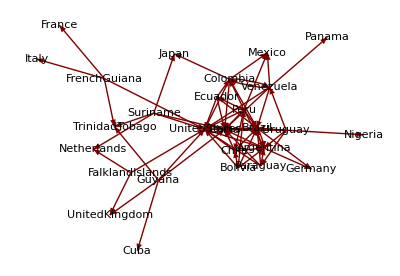

```mathematica
GraphPlot[Flatten[Thread[#->CountryData[#,"ImportPartners"]]&/@CountryData["SouthAmerica"]],VertexLabeling->True,DirectedEdges->True]
```

```mathematica
CountryData["SouthAmerica"]
```

{Argentina,Bolivia,Brazil,Chile,Colombia,Ecuador,FalklandIslands,FrenchGuiana,Guyana,Paraguay,Peru,Suriname,Uruguay,Venezuela}

```mathematica
Graphics[{LightGray,CountryData["Australia","Polygon"],Red,PointSize[.01],Select[Point[Reverse[CityData[#,"Coordinates"]]]&/@CityData[{All,"Australia"}],FreeQ[#,_Missing]&]}];
```

```mathematica
CountryData[#,"ElectricalGridSocketImages"]&/@CountryData[];
```

```mathematica
CountryData[];
```

```mathematica
Graphics[Inset[CountryData[#,"ElectricalGridSocketImages"],{Log[10,CountryData[#,"Population"]],Log[10,CountryData[#,"GDP"]]},Center,0.2]&/@DeleteCases[CountryData["UN"],"VaticanCity"],Frame->True,PlotRangePadding->.2];
```

```mathematica
Graphics[MapIndexed[{ColorData[3][First[#2]],CountryData[#,{"SchematicPolygon","LambertAzimuthal"}]}&,CountryData[]]]
```